```mathematica
(*FIG 3 in PRA 97, 052101 (2018)*)
```

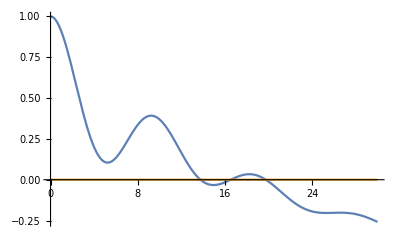

```mathematica
y=1;
l=0.1;
w=10;
d=0.5/y;
sz=1;
a=Sqrt[1-2*y*l/(l+I*d)^2];
A[t_]:=Exp[-I*w*t-1/2*(l+I*d)*t]*(Cosh[(l+I*d)/2*a*t]+1/a*Sinh[(l+I*d)/2*a*t]);
Czz[t2_,t1_]:=1-(Abs[A[t2]]^2+Abs[A[t1]]^2-2*Conjugate[A[t2]]*A[t2-t1]*A[t1])*(1+sz);
Plot[{Re[Czz[t2/y,0]],Im[Czz[t2/y,0]]},{t2,0,30},PlotRange->All]
ClearAll["Global`*"];
```

```mathematica
(*my model*)
```

0.02097

0.0802652

0.1

1.13953+0.0568395 ⅈ

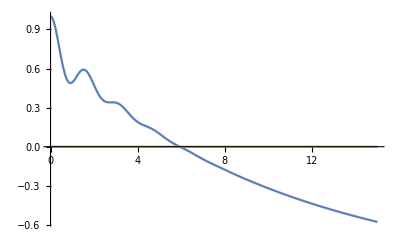

```mathematica
g0=0.02901;
l=0.04194/2
y=2*g0^2/l
w=2.787;
d=0.1
sz=1;
a=Sqrt[1-2*y*l/(l+I*d)^2]
A[t_]:=Exp[-I*w*t-1/2*(l+I*d)*t]*(Cosh[(l+I*d)/2*a*t]+1/a*Sinh[(l+I*d)/2*a*t]);
Czz[t2_,t1_]:=1-(Abs[A[t2]]^2+Abs[A[t1]]^2-2*Conjugate[A[t2]]*A[t2-t1]*A[t1])*(1+sz);
Plot[{Re[Czz[t2/g0,0]],Im[Czz[t2/g0,0]]},{t2,0,15},PlotRange->All]
ClearAll["Global`*"];
```

0.02097

0.0802652

0.1

1.13953+0.0568395 ⅈ

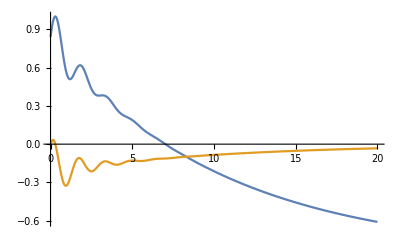

```mathematica
g0=0.02901;
l=0.04194/2
y=2*g0^2/l
w=2.787;
d=0.1
sz=1;
a=Sqrt[1-2*y*l/(l+I*d)^2]
A[t_]:=Exp[-I*w*t-1/2*(l+I*d)*t]*(Cosh[(l+I*d)/2*a*t]+1/a*Sinh[(l+I*d)/2*a*t]);
Czz[t2_,t1_]:=1-(Abs[A[t2]]^2+Abs[A[t1]]^2-2*Conjugate[A[t2]]*A[t2-t1]*A[t1])*(1+sz);
Plot[{Re[Czz[t2/g0,10]],Im[Czz[t2/g0,10]]},{t2,0,20},PlotRange->All]
ClearAll["Global`*"];
```